July 2017

NOTES
In this file, the mutation bias is denoted by p (as in Debarre 2017), instead of ν as in the manuscript. 
Be careful, because in this file, ν is sometimes used to refer to the degree of a graph, but it is always equal to 1 for the subdivided populations that we consider.

Clean the memory

```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

Set path to folder where outputs should be saved

```mathematica
pathtosave="~/Documents/Work/Projects/2016_SocEvolSubdivPop/Programs/";
```

# Generalities - Initializations

## Generic

### Some functions

Function to turn P into Q

```mathematica
PtoQ[P_]:=(P-p^2)/(p(1-p))//FullSimplify;
```

Delta function

```mathematica
Delta[x_]:=If[x==0,1,0]
```

### Define graphs for numerical evaluation

#### Island model, dispersal graph, generic

N = 12

```mathematica
G12generic=({{dself, din, din, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {din, dself, din, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {din, din, dself, dout, dout, dout, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, dself, din, din, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, din, dself, din, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, din, din, dself, dout, dout, dout, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, dself, din, din, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, din, dself, din, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, din, din, dself, dout, dout, dout}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, dself, din, din}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, din, dself, din}, {dout, dout, dout, dout, dout, dout, dout, dout, dout, din, din, dself}});
Nin=3;
Ndemes=4;
```

N = 10

```mathematica
G10generic=({{dself, din, din, din, din, dout, dout, dout, dout, dout}, {din, dself, din, din, din, dout, dout, dout, dout, dout}, {din, din, dself, din, din, dout, dout, dout, dout, dout}, {din, din, din, dself, din, dout, dout, dout, dout, dout}, {din, din, din, din, dself, dout, dout, dout, dout, dout}, {dout, dout, dout, dout, dout, dself, din, din, din, din}, {dout, dout, dout, dout, dout, din, dself, din, din, din}, {dout, dout, dout, dout, dout, din, din, dself, din, din}, {dout, dout, dout, dout, dout, din, din, din, dself, din}, {dout, dout, dout, dout, dout, din, din, din, din, dself}});
```

#### Island model, interaction graph, generic

```mathematica
GE12generic=G12generic/.{dself->eself,dout->eout,din->ein};
GE10generic=G10generic/.{dself->eself,dout->eout,din->ein};
```

#### Generic Q matrix

N = 12

```mathematica
Q12generic=({{1, Qin, Qin, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, 1, Qin, Qin, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin}, {Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1}});
```

N = 10

```mathematica
Q10generic=({{1, Qin, Qin, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, 1, Qin, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, 1, Qin, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, Qin, 1, Qin, Qout, Qout, Qout, Qout, Qout}, {Qin, Qin, Qin, Qin, 1, Qout, Qout, Qout, Qout, Qout}, {Qout, Qout, Qout, Qout, Qout, 1, Qin, Qin, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, 1, Qin, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, 1, Qin, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, Qin, 1, Qin}, {Qout, Qout, Qout, Qout, Qout, Qin, Qin, Qin, Qin, 1}});
```

#### Formulas for d and e

Replacements for the generic dispersal probabilities, depending on whether there is self-replacement or not

```mathematica
noselfreplacement={dself->0,din->(1-m)/(n-1),dout->m/(d n - n)};
withselfreplacement={dself->(1-m)/n,din->(1-m)/n,dout->m/(d n - n)};
```

Replacements for the generic interaction probabilities, depending on whether there is self - interaction or not

```mathematica
groupnoself={eself->0,ein->1/(n-1),eout->0};
groupwithself={eself->1/n,ein->1/n,eout->0};
```

We can even assume that there are a proportion g of interactions outside of the group

```mathematica
widewithself={eself->(1-g)/n,ein->(1-g)/n,eout->g/(n d-n)};
widenoself={eself->0,ein->(1-g)/(n-1),eout->g/(n d-n)};
```

Combine these using Idself and Ieself, indicator variables for whether there is dispersal/interaction with self

```mathematica
genericde={dself->Idself (1-m)/n,din->(1-m)(1/(n-1)-Idself 1/(n(n-1))),dout->m/(n d-n),(*
*)eself->Ieself (1-g)/n,ein->(1-g)(1/(n-1)-Ieself 1/(n(n-1))),eout->g/(n d-n)};
```

```mathematica
eself+(n-1)ein+(n d-n)eout/.genericde//Simplify
dself+(n-1)din+(n d-n)dout/.genericde//Simplify
```

1

1

# Probabilities of identity by descent (Q)

## Moran

### Simplify QinM and QoutM

See Appendix B2 for details on how Qself, Qin and Qout were obtained using a formula presented in the appendix of Debarre 2017 JTB for “2D graphs”.

```mathematica
QselfM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(n-1)+1/(1-(1-μ)(1-m-m/(d-1)))(d-1)+1/(1-(1-μ)(dself-din))(d-1)(n-1));
```

```mathematica
QinM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(-1)+1/(1-(1-μ)(1-m-m/(d-1)))(d-1)+1/(1-(1-μ)(dself-din))(d-1)(-1));
QoutM2=(μ λ)/(n d)(1/μ + 1/(1-(1-μ)(dself-din))(-1)+1/(1-(1-μ)(1-m-m/(d-1)))(-1)+1/(1-(1-μ)(dself-din)));
```

Find λ using Qself == 1

```mathematica
theλM=λ/.Solve[QselfM2==1,λ]⟦1⟧//FullSimplify
```

(n (1+din+dself (-1+μ)-din μ) (-d m+μ+d (-1+m) μ))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

Replace λ in the equations for Qin and Qout

```mathematica
QinM=QinM2/.λ-> theλM//FullSimplify
QoutM=QoutM2/.λ-> theλM//FullSimplify
```

((-1+μ) ((-1+d) (1+din-dself) μ+m (1+din-dself-(d+din-dself) μ)))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

(m (-1+μ) (1+din+dself (-1+μ)-din μ))/(m (-1+μ) (1+din-dself+(-din+dself+d (-1+n)) μ)+(-1+d) μ (-1+dself+din (-1+μ)+μ-(dself+n) μ))

### Check numerically

```mathematica
NGetQM[G_,Ν_,n_,p_,μ_]:=Module[{QT,eqs,vars,sols,QTs},(*
G is the dispersal graph,
Ν is the size of the population,
n is the degree of the graph (=1 in a subdivided population),
p is the mutation biais,
μ is the mutation probability.
*)

(* Initialize the QT matrix *)
Do[Subscript[Q, i,j]=0;Subscript[Q, i,j]=.,{i,1,Ν},{j,1,Ν}];
QT=Table[Subscript[Q, i,j],{i,1,Ν},{j,1,Ν}];
Do[QT⟦i,i⟧=1,{i,1,Ν}]; (* Subscript[Q, i,i]= 1 *)
Do[QT⟦i,j⟧=Subscript[Q, j,i],{j,1,Ν-1},{i,j+1,Ν}]; (* Because Q is symmetric *)

eqs=Flatten[Table[Subscript[Q, i,j]==(1-μ)/(2 n)(Sum[G⟦l,j⟧QT⟦l,i⟧+G⟦l,i⟧QT⟦l,j⟧,{l,1,Ν}]),{i,1,Ν-1},{j,i+1,Ν}]];

vars=Flatten[Table[Subscript[Q, i,j],{i,1,Ν-1},{j,i+1,Ν}]];
sols=NSolve[eqs,vars];

QTs=QT/.sols⟦1⟧;
QTs]
```

```mathematica
prs=.;
CheckQM[prs_,dvalues_]:=Module[{NG,NQin,NQout,NQin12},
NG=G12generic/.dvalues/.prs;
NQin12=NGetQM[NG,n d/.prs,1,0.5,μ/.prs];
NQin=NQin12⟦1,2⟧;
NQout=NQin12⟦1,12⟧;
Print[{{NQin,QinM/.dvalues/.prs},{NQout,QoutM/.dvalues/.prs}}]
]

CheckQM[{m->0.2,d->4,n->3,μ->0.2},withselfreplacement]
CheckQM[{m->0.2,d->4,n->3,μ->0.2},noselfreplacement]
```

{{0.407643,0.407643},{0.127389,0.127389}}

{{0.503735,0.503735},{0.140875,0.140875}}

### Particular cases

#### Equations with self replacement (dself = din)

```mathematica
QinMs=QinM/.withselfreplacement//FullSimplify
QoutMs=QoutM/.withselfreplacement//FullSimplify
```

-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

Simplify the way the equations are written (human - friendly versions), and check that the formulas remain correct

```mathematica
QinMs-((1-μ) (d μ(1-m)-μ+m ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ))//FullSimplify
```

0

```mathematica
QoutMs-(m (1-μ))/((d-1) μ (1+(n-1) μ)+m (1-μ) (1+d (n-1) μ))//FullSimplify
```

0

Check limit behavior

```mathematica
Limit[QoutMs,d->∞]//FullSimplify
Limit[Limit[QoutMs,μ->0],d->∞]//FullSimplify
```

0

1

```mathematica
Limit[QinMs,d->∞]//FullSimplify
%/.μ->0//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

(1-m)/(1+m (-1+n))

```mathematica
Limit[QinMs,μ->0]
Limit[%,d->∞]//FullSimplify
```

1

1

```mathematica
Series[QinMs,{μ,0,1}]
```

1-d n μ+O[μ]^2

#### Equations without Self - replacement (dself = 0)

```mathematica
QinMw=QinM/.noselfreplacement//FullSimplify
QoutMw=QoutM/.noselfreplacement//FullSimplify
```

((-1+μ) (m^2 (-1+μ)+(-1+d) n μ+m (n-d n μ)))/(m^2 (-1+μ)^2-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ))

(m (n+m (-1+μ)-μ) (-1+μ))/(m^2 (-1+μ)^2-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ))

Simplify the way they are written

```mathematica
QinMw-((1-μ) (d n μ(1-m)+(m-μ) n-m^2 (1-μ)))/(+(d-1) n μ (1+(n-2) μ)+m n (1-μ) (1+d (n-2) μ)-m^2 (1-μ)^2)//FullSimplify
```

0

```mathematica
QoutMw-(m (n+m (-1+μ)-μ) (1-μ))/(+(d-1) n μ (1+(n-2) μ)+m n (1-μ) (1+d (n-2) μ)-m^2 (1-μ)^2)//FullSimplify
```

0

Limit behavior

```mathematica
Limit[QinMw,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

(-1+m+μ-m μ)/(-1+m (-2+n) (-1+μ)-(-2+n) μ)

(1-m)/(1+m (-2+n))

```mathematica
Limit[QoutMw,d->∞]
Limit[QoutMw,μ->0]
```

0

1

## Wright - Fisher

### Simplify QinM and QoutM

See Appendix B2 for details on how Qself, Qin and Qout were obtained using a formula presented in the appendix of Debarre 2017 JTB for "2D graphs".

```mathematica
QselfWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)+1/(1-(1-μ)^2(dself-din)^2)(n-1)d+1/(1-(1-μ)^2(1-m-m/(d-1))^2)(d-1));
QinWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)-1/(1-(1-μ)^2(dself-din)^2)d+1/(1-(1-μ)^2(1-m-m/(d-1))^2)(d-1));
QoutWF2=(μ λ)/(n d)(1/(1 - (1-μ)^2)-1/(1-(1-μ)^2(1-m-m/(d-1))^2));
```

Find λ using Qself == 1

```mathematica
λWF=λ/.Solve[QselfWF2==1,λ]⟦1⟧
```

(d n)/((1/(1-(1-μ)^2)+(d (-1+n))/(1-(-din+dself)^2 (1-μ)^2)+(-1+d)/(1-(1-m-m/(-1+d))^2 (1-μ)^2)) μ)

Replace λ in the equations

```mathematica
QinWF=QinWF2/.λ->λWF//FullSimplify
QoutWF=QoutWF2/.λ->λWF//FullSimplify
```

(-d/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((d (-1+n))/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((d (-1+n))/(1-(din-dself)^2 (-1+μ)^2)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

### Check numerically

```mathematica
NGetQWF[G_,Ν_,n_,p_,μ_]:=Module[{QT,eqs,vars,sols,QTs},(*
G is the dispersal graph,
Ν is the size of the population,
n is the degree of the graph (=1 in a subdivided pop),
p is the mutation biais,
μ is the mutation probability.
*)

(* Initialize the QT matrix *)
Do[Subscript[Q, i,j]=0;Subscript[Q, i,j]=.,{i,1,Ν},{j,1,Ν}];
QT=Table[Subscript[Q, i,j],{i,1,Ν},{j,1,Ν}];
Do[QT⟦i,i⟧=1,{i,1,Ν}]; (* Subscript[Q, i,i]=1 *)
Do[QT⟦i,j⟧=Subscript[Q, j,i],{j,1,Ν-1},{i,j+1,Ν}]; (* Because Q is symmetric *)

eqs=Flatten[Table[Subscript[Q, i,j]==(1-μ)^2/n^2(Sum[G⟦l,j⟧G⟦k,i⟧QT⟦k,l⟧,{l,1,Ν},{k,1,Ν}]),{i,1,Ν-1},{j,i+1,Ν}]];

vars=Flatten[Table[Subscript[Q, i,j],{i,1,Ν-1},{j,i+1,Ν}]];
sols=NSolve[eqs,vars];

QTs=QT/.sols⟦1⟧;
QTs]
```

```mathematica
prs=.;
CheckQWF[prs_,dvalues_]:=Module[{NG,NQin,NQout,NQin12},
NG=G12generic/.dvalues/.prs;
NQin12=NGetQWF[NG,n d/.prs,1,0.5,μ/.prs];
NQin=NQin12⟦1,2⟧;
NQout=NQin12⟦1,12⟧;
Print[{{NQin,QinWF/.dvalues/.prs},{NQout,QoutWF/.dvalues/.prs}}]
]

CheckQWF[{m->0.2,d->4,n->3,μ->0.2},withselfreplacement]
CheckQWF[{m->0.2,d->4,n->3,μ->0.2},noselfreplacement]
```

{{0.218352,0.218352},{0.0816154,0.0816154}}

{{0.178044,0.178044},{0.0770357,0.0770357}}

### Particular cases

#### With Self Replacement

```mathematica
QinWFs=QinWF/.withselfreplacement//FullSimplify
```

(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

```mathematica
QoutWFs=QoutWF/.withselfreplacement//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))

Limit behavior

```mathematica
Limit[QinWFs,μ->0]
Limit[QoutWFs,μ->0]
```

1

1

```mathematica
Limit[QinWFs,d->∞]//FullSimplify
Limit[%,μ->0]//FullSimplify
```

-((-1+m)^2 (-1+μ)^2)/(-1-2 m (-1+n) (-1+μ)^2+m^2 (-1+n) (-1+μ)^2+(-1+n) (-2+μ) μ)

-(-1+m)^2/(-1+(-2+m) m (-1+n))

```mathematica
Limit[QoutWFs,d->∞]//FullSimplify
```

0

#### Without Self Replacement

```mathematica
QinWFw=QinWF/.noselfreplacement//FullSimplify
```

((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))

```mathematica
QoutWFw=QoutWF/.noselfreplacement//FullSimplify
```

(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))

# Expected Frequency Equations

## Formulas for the different life-cycles

(Here we just write down the formulas obtained by hand)

### Moran, Birth-Death

#### β

```mathematica
βBDD=(1-μ)(eself+(n-1)ein Qin + (n d-n)eout Qout);
```

```mathematica
βBDI=dself eself + (n-1)din ein+(n d -n )dout eout(*
*)+ (n-1)(din eself + dself ein +(n-2)din ein + (n d -n)dout eout)Qin (*
*)+(n d - n)(dself eout + (n-1)din eout + dout eself+(n-1)dout ein+(n d -2n)dout eout)Qout(*
*)-μ/(n d)(1+(n-1)Qin+(n d -n)Qout)(eself+(n-1)ein+(n d-n)eout);
```

```mathematica
factorBD=(p(1-p))/μ
```

((1-p) p)/μ

```mathematica
βBD=factorBD(βBDD-βBDI);
```

#### γ

```mathematica
γBDD=1-μ;
```

```mathematica
γBDI=dself+(n-1)din Qin+(n d-n)dout Qout-μ/(n d)(1+(n-1)Qin+(n d-n)Qout);
```

```mathematica
γBD=factorBD(γBDD-γBDI)//FullSimplify
```

((-1+p) p (d n (-1+dself+din (-1+n) Qin+(-1+d) dout n Qout)+(-1+Qin+n (d-Qin+Qout-d Qout)) μ))/(d n μ)

### Moran, Death-Birth

#### β

```mathematica
βDBD=βBDD
```

(eself+ein (-1+n) Qin+eout (-n+d n) Qout) (1-μ)

```mathematica
βDBI=(1-μ)(1*dself dself eself*1(*
02*)+(n-1)dself din ein *1(*
03*)+(n d-n)dself dout eout *1(*
04*)+(n-1)dself dself ein Qin(*
05*)+(n-1) dself din eself Qin(*
06*)+(n-1)(n-2)dself din ein Qin(*
07*)+(n-1)(n d-n) dself dout eout Qin(*
08*)+(n d -n)dself dself eout Qout(*
09*)+(n d -n)(n-1) dself din eout Qout(*
10*)+(n d -n)dself dout eself Qout(*
11*)+(n d -n)(n-1) dself dout ein Qout(*
12*)+(n d -n)(n d-2n) dself dout eout Qout(*
13*)+(n-1)din dself eself Qin(*
14*)+(n-1) din din ein Qin(*
15*)+(n-1)(n-2)din din ein Qin (*
16*)+(n-1)(n d -n)din dout eout Qin(*
17*)+(n-1)din dself ein (*
18*)+(n-1)din din eself(*
19*)+(n-1)(n-2)din din ein(*
20*)+(n-1)(n d-n)din dout eout(*
21*)+(n-1)(n-2)din dself ein Qin(*
22*)+(n-1)(n-2)din din ein Qin(*
23*)+(n-1)(n-2) din din eself Qin(*
24*)+(n-1)(n-2)(n-3)din din ein Qin(*
25*)+(n-1)(n-2)(n d-n)din dout eout Qin(*
26*)+(n-1)(n d-n)din dself eout Qout(*
27*)+(n-1)(n d-n)din din eout Qout(*
28*)+(n-1)(n d-n)(n-2)din din eout Qout(*
29*)+(n-1)(n d-n)din dout eself Qout(*
30*)+(n-1)(n d-n)(n-1)din dout ein Qout(*
31*)+(n-1)(n d-n)(n d-2n) din dout eout Qout(*
32*)+(n d-n)dout dself eself Qout(*
33*)+(n d-n)(n-1)dout din ein Qout(*
34*)+(n d-n)dout dout eout Qout(*
35*)+(n d-n)(n-1) dout dout eout Qout(*
36*)+(n d-n)(n d-2n)dout dout eout Qout(*
37*)+(n d-n)(n-1)dout dself ein Qout(*
38*)+(n d-n)(n-1)dout din eself Qout(*
39*)+(n d-n)(n-1)(n-2)dout din ein Qout(*
40*)+(n d -n)(n-1)dout dout eout Qout(*
41*)+(n d-n)(n-1)(n-1)dout dout eout Qout(*
42*)+(n d-n)(n-1)(n d-2n)dout dout eout Qout(*
43*)+(n d-n)dout dself eout (*
44*)+(n d-n)(n-1)dout din eout(*
45*)+(n d-n)dout dout eself(*
46*)+(n d-n)(n-1)dout dout ein(*
47*)+(n d-n)(n d-2n)dout dout eout(*
48*)+(n d-n)(n-1)dout dself eout Qin(*
49*)+(n d-n)(n-1)(n-1)dout din eout Qin(*
50*)+(n d-n)(n-1)dout dout ein Qin(*
51*)+(n d-n)(n-1)dout dout eself Qin(*
52*)+(n d-n)(n-1)(n-2)dout dout ein Qin(*
53*)+(n d-n)(n-1)(n d-2n)dout dout eout Qin(*
54*)+(n d-n)(n d-2n)dout dself eout Qout(*
55*)+(n d-n)(n d-2n)(n-1)dout din eout Qout(*
56*)+(n d-n)(n d-2n)dout dout eout Qout(*
57*)+(n d-n)(n d-2n)(n-1)dout dout eout Qout(*
58*)+(n d-n)(n d-2n)dout dout eself Qout(*
59*)+(n d-n)(n d-2n)(n-1)dout dout ein Qout(*
60*)+(n d-n)(n d-2n)(n d-3n)dout dout eout Qout);
```

```mathematica
factorDB=factorBD
```

((1-p) p)/μ

```mathematica
βDB=factorDB(βDBD-βDBI)//FullSimplify
```

1/μ(1-p) p (eself+ein (-1+n) Qin+(-1+d) eout n Qout-dself^2 (eself+ein (-1+n) Qin+(-1+d) eout n Qout)-din^2 (-1+n) (eself+eself (-2+n) Qin+ein (-2+n+(3+(-3+n) n) Qin)+(-1+d) eout (-1+n) n Qout)-(-1+d) dout^2 n ((eself+ein (-1+n)+(-2+d) eout n) (1+(-1+n) Qin)+n ((-2+d) eself+(-2+d) ein (-1+n)+(3+(-3+d) d) eout n) Qout)-2 (-1+d) dout dself n ((eself+ein (-1+n)) Qout+eout (1+(-1+n) Qin+(-2+d) n Qout))-2 din (-1+n) (dself (ein+eself Qin+ein (-2+n) Qin+(-1+d) eout n Qout)+(-1+d) dout n (eout+eout (-1+n) Qin+(eself+ein (-1+n)+(-2+d) eout n) Qout))) (1-μ)

#### γ

```mathematica
γDBD=γBDD
```

1-μ

```mathematica
γDBI=(1-μ)(dself^2+(n-1)din^2+(n d-n)dout^2(*
*)+(n-1)(dself din+ din dself+(n-2)din din + (n d-n)dout dout)Qin(*
*)+(n d-n)(dself dout +(n-1)din dout+ dout dself+ (n-1)dout din+(n d-2n)dout dout)Qout);
```

```mathematica
γDB=factorDB(γDBD-γDBI)
```

((1-p) p (1-(dself^2+din^2 (-1+n)+dout^2 (-n+d n)+(-1+n) (2 din dself+din^2 (-2+n)+dout^2 (-n+d n)) Qin+(-n+d n) (2 dout dself+2 din dout (-1+n)+dout^2 (-2 n+d n)) Qout) (1-μ)-μ))/μ

### Wright - Fisher

#### β

```mathematica
βWF=βDB;
```

#### γ

```mathematica
γWF=γDB;
```

## Check the results numerically

We use generic equations valid for any life-cycle and any graph, and adapt them to our life-cycles and to a subdivided population. We compare the numerical results to the ones obtained with the equations written above.

### Full functions, any life-cycle

β and γ were calculated by hand - these are generic equations value for any life-cycle and any regular graph. 
(see Appendix for details, and Debarre 2017 JTB for even further details)

```mathematica
GetBeta[sBf_,Df_,G_,GE_,Qmat_,Ν_,ν_,Bstar_]:=Module[{part1,part2,factor},
factor=(p(1-p))/(μ Ν Bstar);
part1=Sum[((1-μ)sBf[G,Ν,ν,j,l]-Df[G,Ν,ν,j,l])*GE⟦k,l⟧*Qmat⟦j,k⟧,{j,1,Ν},{k,1,Ν},{l,1,Ν}];
factor*part1]

GetGamma[sBf_,Df_,G_,GE_,Qmat_,Ν_,ν_,Bstar_]:=Module[{part1,part2,factor},
factor=(p(1-p))/(μ Ν Bstar);part1=Sum[((1-μ)sBf[G,Ν,ν,j,k]-Df[G,Ν,ν,j,k])*Qmat⟦j,k⟧,{j,1,Ν},{k,1,Ν}];
factor*part1]
```

### Moran DB

#### Define δB and δD

ν is the degree of the graph, here equal to 1

```mathematica
sBfDB[G_,Ν_,ν_,j_,k_]:=(Delta[k-j] ν^2-Sum[G⟦j,i⟧G⟦k,i⟧,{i,1,Ν}])/(Ν ν^2);
DfDB[G_,Ν_,ν_,j_,k_]:=0;
BstarDB=1/Ν;
```

#### β

```mathematica
βDBexemple=GetBeta[sBfDB,DfDB,G12generic,GE12generic,Q12generic,12,1,BstarDB/.Ν->12]//FullSimplify
```

-1/μ(-1+p) p ((-1+dself^2) (eself+2 ein Qin+9 eout Qout)+2 din^2 (ein+eself+3 ein Qin+eself Qin+18 eout Qout)+18 dout dself (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout)+9 dout^2 ((2 ein+6 eout+eself) (1+2 Qin)+3 (4 ein+21 eout+2 eself) Qout)+4 din (dself (ein+(ein+eself) Qin+9 eout Qout)+9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout))) (-1+μ)

```mathematica
βDBexemple-βDB/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βDBexemple2=GetBeta[sBfDB,DfDB,G10generic,GE10generic,Q10generic,10,1,BstarDB/.Ν->10]//FullSimplify
```

-1/μ(-1+p) p ((-1+dself^2) (eself+4 ein Qin+5 eout Qout)+4 din^2 (eself+3 eself Qin+ein (3+13 Qin)+20 eout Qout)+5 dout^2 ((4 ein+eself) (1+4 Qin)+25 eout Qout)+10 dout dself (eout+4 eout Qin+(4 ein+eself) Qout)+8 din (dself (ein+3 ein Qin+eself Qin+5 eout Qout)+5 dout (eout+4 eout Qin+4 ein Qout+eself Qout))) (-1+μ)

```mathematica
βDBexemple2-βDB/.{n->5,d->2}//FullSimplify
```

0

#### γ

```mathematica
γDBexemple=GetGamma[sBfDB,DfDB,G12generic,GE12generic,Q12generic,12,1,BstarDB/.Ν->12]//FullSimplify
```

-((-1+p) p (-1+dself^2+2 din^2 (1+Qin)+4 din (dself Qin+9 dout Qout)+9 dout (dout+2 dout Qin+6 dout Qout+2 dself Qout)) (-1+μ))/μ

```mathematica
γDBexemple-γDB/.{n->3,d->4}//FullSimplify
```

0

```mathematica
γDBexemple2=GetGamma[sBfDB,DfDB,G10generic,GE10generic,Q10generic,10,1,BstarDB/.Ν->10]//FullSimplify
```

-((-1+p) p (-1+dself^2+4 din^2 (1+3 Qin)+8 din (dself Qin+5 dout Qout)+5 dout (dout+4 dout Qin+2 dself Qout)) (-1+μ))/μ

```mathematica
γDBexemple2-γDB/.{n->5,d->2}//FullSimplify
```

0

### Moran BD

#### Define δB and δD

```mathematica
sBfBD[G_,Ν_,ν_,j_,k_]:=(Delta[k-j]Ν-1)/Ν^2 ;
DfBD[G_,Ν_,ν_,j_,k_]:=G⟦k,j⟧/(Ν ν)-1/Ν^2;
BstarBD=1/Ν;
```

#### Equations β

```mathematica
βBDexemple=GetBeta[sBfBD,DfBD,G12generic,GE12generic,Q12generic,12,1,BstarBD/.Ν->12]//FullSimplify
```

1/(12 μ)(-1+p) p (12 ((-1+dself) (eself+2 ein Qin+9 eout Qout)+2 din (ein+(ein+eself) Qin+9 eout Qout)+9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout))+(-9 eout+11 eself-2 (ein-10 ein Qin+(9 eout+eself) Qin)-9 (2 ein-3 eout+eself) Qout) μ)

```mathematica
βIBDtest=Sum[(μ/Ν^2-G⟦l,j⟧/Ν)GE⟦k,l⟧Q⟦j,k⟧,{j,1,Ν},{k,1,Ν},{l,1,Ν}]/.{G->G12generic,GE->GE12generic,Q->Q12generic,Ν->12}//FullSimplify
```

Part::pkspec1: The expression l cannot be used as a part specification.

Part::pkspec1: The expression k cannot be used as a part specification.

Part::pkspec1: The expression j cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-dself (eself+2 ein Qin+9 eout Qout)-2 din (ein+(ein+eself) Qin+9 eout Qout)-9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout)+1/12 (2 ein+9 eout+eself) (1+2 Qin+9 Qout) μ

```mathematica
βIBDtest+βBDI/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βDBDtest=Sum[(1-μ)/Ν GE⟦k,l⟧Q⟦l,k⟧,{k,1,Ν},{l,1,Ν}]/.{G->G12generic,GE->GE12generic,Q->Q12generic,Ν->12}//FullSimplify
```

Part::pkspec1: The expression k cannot be used as a part specification.

Part::pkspec1: The expression l cannot be used as a part specification.

Part::pkspec1: The expression k cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-(eself+2 ein Qin+9 eout Qout) (-1+μ)

```mathematica
βDBDtest-βBDD/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBDtest=(p(1-p))/μ(βDBDtest+βIBDtest)//FullSimplify
```

1/μ(1-p) p (-dself (eself+2 ein Qin+9 eout Qout)-2 din (ein+(ein+eself) Qin+9 eout Qout)-9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout)-(eself+2 ein Qin+9 eout Qout) (-1+μ)+1/12 (2 ein+9 eout+eself) (1+2 Qin+9 Qout) μ)

```mathematica
βBDtest-βBD/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBDD-βDBDtest/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBDI+βIBDtest/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBDD-βBDI-(βDBDtest+βIBDtest)/.{n->3,d->4}//FullSimplify
```

0

```mathematica
βBD-p(1-p)/μ(βBDD-βBDI)
```

0

```mathematica
βBDexemple-βBDtest//FullSimplify
%/.withselfreplacement//FullSimplify
```

0

0

#### Equations γ

```mathematica
γBDexemple=GetGamma[sBfBD,DfBD,G12generic,GE12generic,Q12generic,12,1,BstarBD/.Ν->12]//FullSimplify
```

((-1+p) p (12 (-1+dself+2 din Qin+9 dout Qout)+(11-2 Qin-9 Qout) μ))/(12 μ)

```mathematica
γBDexemple-γBD/.{n->3,d->4}//Simplify
```

0

### Wright-Fisher

#### Define δB and δD

```mathematica
sBfWF[G_,Ν_,ν_,j_,k_]:=(Delta[k-j] ν^2-Sum[G⟦j,i⟧G⟦k,i⟧,{i,1,Ν}])/ν^2 ;
DfWF[G_,Ν_,ν_,j_,k_]:=0;
BstarWF=1;
```

#### Equations β

```mathematica
βWFexemple=GetBeta[sBfWF,DfWF,G12generic,GE12generic,Q12generic,12,1,BstarWF/.Ν->12]//FullSimplify
```

-1/μ(-1+p) p ((-1+dself^2) (eself+2 ein Qin+9 eout Qout)+2 din^2 (ein+eself+3 ein Qin+eself Qin+18 eout Qout)+18 dout dself (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout)+9 dout^2 ((2 ein+6 eout+eself) (1+2 Qin)+3 (4 ein+21 eout+2 eself) Qout)+4 din (dself (ein+(ein+eself) Qin+9 eout Qout)+9 dout (eout+2 eout Qin+2 ein Qout+6 eout Qout+eself Qout))) (-1+μ)

```mathematica
βWFexemple-βWF/.{n->3,d->4}//Simplify
```

0

#### Equations γ

```mathematica
γWFexemple=GetGamma[sBfWF,DfWF,G12generic,GE12generic,Q12generic,12,1,BstarWF/.Ν->12]//FullSimplify
```

-((-1+p) p (-1+dself^2+2 din^2 (1+Qin)+4 din (dself Qin+9 dout Qout)+9 dout (dout+2 dout Qin+6 dout Qout+2 dself Qout)) (-1+μ))/μ

```mathematica
γWFexemple-γWF/.{n->3,d->4}//Simplify
```

0

## Generic

```mathematica
EX[β_,γ_,b_,c_,p_,δ_]:=p+δ(b β -c γ)
```

```mathematica
EXBD=p+δ(βBD b - γBD c)/.{Qin->QinM,Qout->QoutM}/.genericde//Simplify
```

(p ((b-c) (-1+p) δ μ (m-n+Idself (-1+m) (-1+μ)+μ-m μ)+d^2 (-c Idself m n δ-c m^2 n δ+c Idself m^2 n δ+c m n^2 δ+c Idself m n p δ+c m^2 n p δ-c Idself m^2 n p δ-c m n^2 p δ+Idself μ-Idself m μ-n μ+2 m n μ-m n^2 μ+2 c Idself δ μ-2 c Idself m δ μ-2 c n δ μ-c Idself n δ μ+2 c m n δ μ+2 c Idself m n δ μ+c m^2 n δ μ-c Idself m^2 n δ μ+c n^2 δ μ-2 c m n^2 δ μ-2 c Idself p δ μ+2 c Idself m p δ μ+2 c n p δ μ+c Idself n p δ μ-2 c m n p δ μ-2 c Idself m n p δ μ-c m^2 n p δ μ+c Idself m^2 n p δ μ-c n^2 p δ μ+2 c m n^2 p δ μ-Idself μ^2+Idself m μ^2+2 n μ^2-2 m n μ^2-n^2 μ^2+m n^2 μ^2-c Idself δ μ^2+c Idself m δ μ^2+2 c n δ μ^2-2 c m n δ μ^2-c n^2 δ μ^2+c m n^2 δ μ^2+c Idself p δ μ^2-c Idself m p δ μ^2-2 c n p δ μ^2+2 c m n p δ μ^2+c n^2 p δ μ^2-c m n^2 p δ μ^2+b (-1+g) (-1+p) δ (-Ieself (m (-1+μ)-μ) (m+n (-1+μ)-μ)+(-1+m) n (-2+μ) μ+Idself (-1+m) (Ieself (m (-1+μ)-μ)-(-2+μ) μ)))+d (m^2 (-1+μ) (-1+c (-1+p) δ+b (δ-p δ)+μ)+μ ((c+b (-1+(-1+g) Ieself)) (-1+p) δ μ+n (1+3 c δ-3 c p δ-2 μ-2 c δ μ+2 c p δ μ-b (-1+p) δ (-3+Ieself+g (2+Ieself (-1+μ)-μ)+μ-Ieself μ))+n^2 (μ+c δ (-1+p+μ-p μ)))+m (n (b (δ-p δ)-(-1+c (-1+p) δ) (-1+μ))-(-1+p) δ μ (2 c (-1+μ)+b (2-Ieself-2 μ+g (-2+Ieself+μ))))+Idself (-1+m) (m (1+b (-1+p) δ+c (δ-p δ)-μ) (-1+μ)+μ (1-μ+c (-1+p) δ (-3+n+2 μ)+b (-1+p) δ (3-Ieself-2 μ+g (-2+Ieself+μ)))))))/(d (m^2 (-1+μ)^2-Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)-(-1+d) n μ (1+(-2+n) μ)+m n (-1+μ) (1+d (-2+n) μ)))

```mathematica
EXDB=p+δ(βDB b - γDB c)/.{Qin->QinM,Qout->QoutM}/.genericde//Simplify
```

(p ((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ))+(-1+d)^2 n^3 (1-p) δ (-1+μ) (c (-1+d) (-1+n) (m n (2+d (n (-1+μ)-2 μ))-(-1+d) (-2+n) n μ+m^2 (-2+d n+μ)-Idself^2 (-1+m)^2 (d (m (-1+μ)-μ)+μ)+Idself (-1+m) (d m^2 (-1+μ)+2 (-1+d) μ+m (2-2 d μ)))+b (2 m^2-2 d m^2-2 d Ieself m^2+2 d^2 Ieself m^2+2 d g Ieself m^2-2 d^2 g Ieself m^2+d g m^3+d Ieself m^3-d^2 Ieself m^3-d g Ieself m^3+d^2 g Ieself m^3-2 m n+2 d m n+2 d Ieself m n-2 d^2 Ieself m n-2 d g Ieself m n+2 d^2 g Ieself m n-2 m^2 n+3 d m^2 n-d^2 m^2 n-2 d g m^2 n+d^2 g m^2 n-d m^3 n+d^2 m^3 n-d^2 g m^3 n+2 m n^2-3 d m n^2+d^2 m n^2+d g m n^2-d^2 g m n^2-d Ieself m n^2+d^2 Ieself m n^2+d g Ieself m n^2-d^2 g Ieself m n^2+d m^2 n^2-d^2 m^2 n^2+d^2 g m^2 n^2+2 g m μ-2 d g m μ+2 Ieself m μ-4 d Ieself m μ+2 d^2 Ieself m μ-2 g Ieself m μ+4 d g Ieself m μ-2 d^2 g Ieself m μ-m^2 μ+d m^2 μ-g m^2 μ+2 d g m^2 μ-Ieself m^2 μ+4 d Ieself m^2 μ-3 d^2 Ieself m^2 μ+g Ieself m^2 μ-4 d g Ieself m^2 μ+3 d^2 g Ieself m^2 μ-d g m^3 μ-d Ieself m^3 μ+d^2 Ieself m^3 μ+d g Ieself m^3 μ-d^2 g Ieself m^3 μ+2 n μ-4 d n μ+2 d^2 n μ-2 g n μ+4 d g n μ-2 d^2 g n μ-2 Ieself n μ+4 d Ieself n μ-2 d^2 Ieself n μ+2 g Ieself n μ-4 d g Ieself n μ+2 d^2 g Ieself n μ-2 m n μ+6 d m n μ-4 d^2 m n μ-4 d g m n μ+4 d^2 g m n μ-2 d Ieself m n μ+2 d^2 Ieself m n μ+2 d g Ieself m n μ-2 d^2 g Ieself m n μ+2 m^2 n μ-5 d m^2 n μ+3 d^2 m^2 n μ+2 d g m^2 n μ-3 d^2 g m^2 n μ+d m^3 n μ-d^2 m^3 n μ+d^2 g m^3 n μ-n^2 μ+2 d n^2 μ-d^2 n^2 μ+g n^2 μ-2 d g n^2 μ+d^2 g n^2 μ+Ieself n^2 μ-2 d Ieself n^2 μ+d^2 Ieself n^2 μ-g Ieself n^2 μ+2 d g Ieself n^2 μ-d^2 g Ieself n^2 μ-d m n^2 μ+d^2 m n^2 μ+d g m n^2 μ-d^2 g m n^2 μ+d Ieself m n^2 μ-d^2 Ieself m n^2 μ-d g Ieself m n^2 μ+d^2 g Ieself m n^2 μ-(-1+d) (-1+g) Idself^2 (-1+Ieself) (-1+m)^2 (d (m (-1+μ)-μ)+μ)+Idself (-1+m) (d m^2 (-1-2 g (-1+Ieself)+2 Ieself+d (-1+g) (-1+2 Ieself-n)-n) (-1+μ)+2 (-1+d)^2 (-1+g) (-1+Ieself) μ-2 (-1+d) m (-1+n+g μ+Ieself μ-g Ieself μ-n μ-d (-1+g) (Ieself+n (-1+μ)+μ-2 Ieself μ)))))))/((-1+n) (n-d n)^3 (-m^2 (-1+μ)^2+Idself (-1+m) (-1+μ) (m (-1+μ)+μ-d μ)+(-1+d) n μ (1+(-2+n) μ)-m n (-1+μ) (1+d (-2+n) μ)))

```mathematica
EXWF=p+δ(βWF b - γWF c)/.{Qin->QinWF,Qout->QoutWF}/.genericde//Simplify
```

p+1/μ(1-p) p δ (-c (1-μ-(1-μ) ((Idself^2 (-1+m)^2)/n^2+((-1+m)^2 (Idself-n)^2)/((-1+n) n^2)+m^2/((-1+d) n)-((2+d (-2+m)) m (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((2 (-1+d) Idself (-1+m)^2-(-1+d) Idself^2 (-1+m)^2+(-1+d) (-2+n) n-2 (-1+d) m (-2+n) n+m^2 (1+d (-2+n) n)) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d) (-1+n) n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))+b (1-μ) ((Ieself-g Ieself)/n+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))-((1-g) (Ieself-n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))-((Idself-Idself m)^2 ((Ieself-g Ieself)/n+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))-((1-g) (Ieself-n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/n^2-(m^2 (((2-3 d+d^2+g) n (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(-1+d-g) (1+((-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/((-1+d)^2 n)-(2 Idself (1-m) m (((1-g) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(g (1+((-2+d) n (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))/((-1+d) n)))/n-1/((-1+n) n^2)(-1+m)^2 (Idself-n)^2 ((Ieself-g Ieself)/n+(g (-1+n) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((1-g) Ieself (-2+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((1-g) (Ieself-n) (-2+n+((3+(-3+n) n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))))/(n-n^2))+1/n 2 (1-m) (Idself-n) ((m (g/n+((-1+d-g) (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+(g (-1+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))/(-1+d)+1/n Idself (1-m) (((-1+g) (Ieself-n))/((-1+n) n)+(g (-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2)))/((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2))+((1-g) Ieself ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/(n ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))+((1-g) (Ieself-n) (-2+n) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)-d/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))/((n-n^2) ((-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+(d (-1+n))/(1-((-1+Idself)^2 (-1+m)^2 (-1+μ)^2)/(-1+n)^2)+1/(2 μ-μ^2)))))))

#### Export to R

Rewrite the Greek letters

```mathematica
GreekTerms={δ->sel, μ->mut}
```

{δ→sel,μ→mut}

Common parts to all functions

```mathematica
FunctionPartB=" <- function(b, c, p, sel, mut, m, g, n, d, Idself, Ieself){
## Arguments:
#  b   benefit of interaction
#  c   cost of interaction
#  p   mutation bias
#  sel intensity of selection
#  mut mutation probability
#  m   emigration probability
#  g   proportion of interactions out of the group (interaction equivalent of m)
#  n   deme size
#  d   number of demes
#  Idself whether reproduction in site where the parent is
#  Ieself whether interactions with oneself
return(
";
FunctionPartE=")
}";
```

Function to translate Mathematica to R

```mathematica
ToRForm[x_]:=ToString[x/.GreekTerms//CForm]
```

Do it for all life cycles

```mathematica
RtxtBD="pBD "<>FunctionPartB<>ToRForm[EXBD]<>FunctionPartE;
RtxtDB="pDB "<>FunctionPartB<>ToRForm[EXDB]<>FunctionPartE;
RtxtWF="pWF "<>FunctionPartB<>ToRForm[EXWF]<>FunctionPartE;
```

Define Power function in R

```mathematica
PowerDef="Power <- function(a,b) return(a^b)";
```

Combine all texts

```mathematica
Rtxt=PowerDef<>"

"<>RtxtBD<>"

"<>RtxtDB<>"

"<>RtxtWF;
```

Export to txt file (Mathematica did not want R)

```mathematica
Export[pathtosave<>"Mathematica/analytics.txt",Rtxt];
```

Convert the file extension to R

```mathematica
cmd="mv"<>" "<> pathtosave<>"Mathematica/analytics.txt "<>pathtosave<>"Mathematica/analytics.R";
```

```mathematica
Get["!"<>cmd];
```

# Changes with m

Here, we consider a population structure 
- with no social interactions with oneself (eself = 0), 
- such that an offspring can establish at the very site of its parent and replace it (dself > 0),
- with social interactions strictly within a deme (g = 0).

```mathematica
mychange=genericde/.Idself->1/.Ieself->0/.g->0;
ApplyParms[x_]:=x/.genericde/.Idself->1/.Ieself->0/.g->0
```

## Probabilities of identity by descent change with the emigration probability m

### Moran

Slopes

```mathematica
D[QinMs,m]//FullSimplify
```

((-1+d)^2 n (-1+μ) μ^2)/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

It is negative for Qin

```mathematica
D[QoutMs,m]//FullSimplify
```

-((-1+d) (-1+μ) μ (1+(-1+n) μ))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

It is positive for Qout.

### Wright - Fisher

Slopes

```mathematica
dqw=D[QinWFs,m]//FullSimplify
```

(2 (-1+d)^3 (1+d (-1+m)) n (-2+μ)^2 (-1+μ)^2 μ^2)/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

```mathematica
Solve[dqw==0,m]//FullSimplify
```

{{m→(-1+d)/d}}

```mathematica
dqw/.m->0//FullSimplify
dqw/.m->1//FullSimplify
```

-(2 n (-1+μ)^2)/(-1+(-1+n) (-2+μ) μ)^2

(2 (-1+d)^3 n μ^2 (2-3 μ+μ^2)^2)/((-2-d^2 n (-2+μ) μ+(-2+μ) μ (-3+(-1+n) (-2+μ) μ)+d (1+(1+2 n) (-2+μ) μ))^2)

The slope of QinWF is negative until mc=(d-1)/d, positive after.

```mathematica
dqwo=D[QoutWFs,m]//FullSimplify
```

-(2 (-1+d)^2 (1+d (-1+m)) (-2+μ) (-1+μ)^2 μ (-1+(-1+n) (-2+μ) μ))/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

```mathematica
Solve[dqwo==0,m]//FullSimplify
```

{{m→(-1+d)/d}}

And it is the opposite for QoutWF.

## BD life-cycle

### β indirect

```mathematica
bi=βBDI/.{Qin->QinM, Qout->QoutM}/.mychange//FullSimplify
```

(-d m+d (1+d (-1+m)+m) μ+(-1+d-d m) μ^2)/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))

```mathematica
dbi=D[bi,m]//FullSimplify
```

-((-1+d)^2 (1+d n-μ) μ^2)/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)

Decreases with m

### EX

```mathematica
ex=EXBD//ApplyParms//FullSimplify
```

-1/(d (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ)))p ((b-c) (-1+p) δ μ+d (m+(b-c) m (-1+p) δ-(1+m+(3 b+c (-3+n)) (-1+p) δ) μ+(1-n+(b+c (-1+n)) (-1+p) δ) μ^2)+d^2 (c m n (-1+p) δ+μ+(m (-1+n)-(2 (b-c) (-1+m)+c (-1+2 m) n) (-1+p) δ) μ+(-1+m) (1-n+(b+c (-1+n)) (-1+p) δ) μ^2))

```mathematica
dex=D[ex,m]//FullSimplify
```

((-1+d)^2 (-1+p) p δ μ (c+c d n-c μ+b (-1+(1+d n (-2+μ)) μ)))/(d ((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2)

```mathematica
Solve[dex==0,m]
```

{}

EX is a monotonic function of m. Increasing or decreasing? This depends on μ:

```mathematica
muc=Solve[dex==0,μ]//FullSimplify
```

{{μ→0},{μ→-(b-c-2 b d n+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n)},{μ→(c+b (-1+2 d n)+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n)}}

We want the middle one

```mathematica
mucc=μ/.muc⟦2⟧//FullSimplify;
```

Simplify in more human form

```mathematica
1-(b-c+√((b-c) (b-c+4 b d^2 n^2)))/(2 b d n)-mucc//FullSimplify
```

0

```mathematica
dex/.μ->1//FullSimplify
```

-((b-c) (-1+p) p δ)/n

Increasing when μ > mucc, decreasing otherwise (but flat when μ = 0).

## DB life - cycle

### β indirect

```mathematica
bi=βDBI/.{Qin->QinM, Qout->QoutM}/.mychange//FullSimplify
```

((-1+μ) (m+(1+d (-1+m)) (-1+m) μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
dbi=D[bi,m]//FullSimplify
```

((-1+μ) (-(-1+μ) (m+(1+d (-1+m)) (-1+m) μ) (1+d (-1+n) μ)+(1+(1+2 d (-1+m)) μ) (-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))))/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2

```mathematica
mcs=Solve[dbi==0,m]//FullSimplify
```

{{m→((-1+d) d (-1+μ) μ (1+(-1+n) μ)-√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2)))/(d (-1+μ)^2 (1+d (-1+n) μ))},{m→((-1+d) d (-1+μ) μ (1+(-1+n) μ)+√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2)))/(d (-1+μ)^2 (1+d (-1+n) μ))}}

the first term is negative -> not solution

```mathematica
mcDBI=m/.mcs⟦2⟧;
```

Second derivative

```mathematica
D[bi,m,m]/.m->mcDBI//FullSimplify
```

(2 d^2 (-1+μ)^2 μ)/(√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2)))

It is a minimum.

```mathematica
Limit[mcDBI,μ->0]
```

0

```mathematica
ddd=mcDBI-(d-1)/d//FullSimplify
```

(1+(√((-1+d)^2 d (-1+μ)^2 μ (n+(-1+μ)^2+d n^2 μ-n μ^2))+d (-1+μ) (1+μ (-2+d n+μ-n μ)))/((-1+μ)^2 (1+d (-1+n) μ)))/d

```mathematica
Solve[ddd==0]
```

{{d→1}}

Constant sign (d > 1). Same sign as when μ->0, i.e. <0
mcDBI < (d-1)/d.

### EX

```mathematica
ex=EXDB//ApplyParms//FullSimplify
```

(p ((b-c) d m^2 (-1+p) δ (-1+μ)+(-1+d) μ (-1+b (-1+p) δ (-1+μ)+c (-1+n) (-1+p) δ (-1+μ)+μ-n μ)-m (-1+μ) (-1+d μ-d n μ+b (-1+p) δ (-2+d+d μ)+c (-1+p) δ (2-d (1+n)+d (-1+n) μ))))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ))

```mathematica
dex=D[ex,m]//FullSimplify
```

1/((-1+d) μ (1+(-1+n) μ)-m (-1+μ) (1+d (-1+n) μ))^2(-1+p) p δ (-1+μ) (c (d m^2+(-1-n+d (-m (2+m)+2 (1+n)+d (-1+m) (1+m (-1+n)+n))) μ-(1+d (-1+m))^2 (-1+n) μ^2)+b (-d m^2+μ+d (-2+m (2+m)+d (1+m (-2+m-m n))) μ+(-(1+d (-1+m))^2+(2+2 d (-2+m)+d^2 (2+(-2+m) m)) n) μ^2))

#### Initial increase?

Close to m=0

```mathematica
dex0=dex/.m->0//FullSimplify
```

((-1+p) p δ (-1+μ) (b+b (-1+2 n) μ-c (1+n+(-1+n) μ)))/(μ (1+(-1+n) μ)^2)

```mathematica
muc0=Solve[dex0==0,μ]//FullSimplify
```

{{μ→1},{μ→(-b+c+c n)/(c-c n+b (-1+2 n))}}

Increases initially if μ>μc, and μc<0 if b>c(n+1).

```mathematica
Limit[dex0,μ->0]//FullSimplify
```

(-1+p) p δ DirectedInfinity[-b+c+c n]

```mathematica
Solve[(μ/.muc0⟦2⟧)==0,b]
```

{{b→c (1+n)}}

```mathematica
Limit[(μ/.muc0⟦2⟧),b->∞]
```

1/(1-2 n)

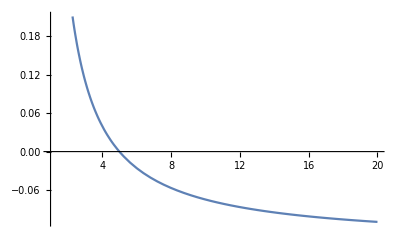

```mathematica
Plot[(μ/.muc0⟦2⟧/.c->1/.n->4),{b,1,20}]
```

#### Maximum

```mathematica
mcs=Solve[dex==0,m]//FullSimplify
```

{{m→((-1+d) (-1+μ) μ (1+(-1+n) μ)-(√(-(b-c) (-1+d)^2 d (-1+p)^2 (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))))/((b-c) d (-1+p)))/((-1+μ)^2 (1+d (-1+n) μ))},{m→((-1+d) (-1+μ) μ (1+(-1+n) μ)+(√(-(b-c) (-1+d)^2 d (-1+p)^2 (-1+μ)^2 μ (c (1+n)+c μ (-2+d n^2+μ-n μ)+b (-1+μ (2-μ+n (2 (-1+μ)+d (-1+(-1+n) (-2+μ) μ)))))))/((b-c) d (-1+p)))/((-1+μ)^2 (1+d (-1+n) μ))}}

Admissible solution is the first one (note (-1+p) at the denominator)

```mathematica
mmax=m/.mcs⟦1⟧;
```

```mathematica
Limit[mmax,μ->0]
```

0

```mathematica
exmax=ex/.m->mmax;
```

## WF life-cycle

### β indirect

```mathematica
bi=βWFI/.{Qin->QinWF, Qout->QoutWF}/.mychange//FullSimplify
```

((-1+μ) ((2+d (-2+m)) m-2 (1+d (-1+m))^2 μ+(1+d (-1+m))^2 μ^2))/((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))

```mathematica
dbi=D[bi,m]//FullSimplify
```

-(2 (-1+d)^3 (1+d (-1+m)) n (-2+μ)^2 (-1+μ) μ^2)/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

```mathematica
Solve[dbi==0,m]//FullSimplify
```

{{m→(-1+d)/d}}

```mathematica
dbi/.m->0//FullSimplify
```

(2 n (-1+μ))/(-1+(-1+n) (-2+μ) μ)^2

Decreases until m=(d-1)/d, then increases

### EX

```mathematica
ex=EXWF//ApplyParms;
```

```mathematica
dex=D[ex,m]//FullSimplify
```

(2 (-1+d)^3 (1+d (-1+m)) n (-1+p) p δ (-2+μ)^2 (-1+μ) μ (c+b (-2+μ) μ))/(((-1+d)^2 (-2+μ) μ (-1+(-1+n) (-2+μ) μ)-2 (-1+d) m (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ)+d m^2 (-1+μ)^2 (-1+d (-1+n) (-2+μ) μ))^2)

```mathematica
Solve[dex==0,m]//FullSimplify
ddex=D[ex,{m,2}]/.%⟦1⟧
```

{{m→(-1+d)/d}}

((1-p) p δ (c (1-μ) (2/n^2+(2 (1-n)^2)/((-1+n) n^2)+2/((-1+d) n)-(2 d (1))/(-1+d)-((2+(-2+1/d) d) (1))/(-1+d)+(1/(d (-1+n)+(-1+d)/(1-1)+1/(2 μ-μ^2))-1+((-1+1/d)^2 (-1+d)+(-1+d) (-2+n) n-1/d+(1^2 1)/d^2) (1) (1))/((-1+d) (-1+n) n))+b (1-μ) (-(8 3)/1+22+1/n)))/μ
 |  |  |  |

```mathematica
Solve[ddex==0,μ]//FullSimplify
```

{{μ→0},{μ→1},{μ→2},{μ→2},{μ→1-(√(b (b-c)))/b},{μ→(b+√(b (b-c)))/b}}

```mathematica
dex0=dex/.m->0//FullSimplify
Solve[%==0,μ]
Limit[dex0,μ->0]
```

-(2 n (-1+p) p δ (-1+μ) (c+b (-2+μ) μ))/(μ (-1+(-1+n) (-2+μ) μ)^2)

{{μ→1},{μ→(b-√(b^2-b c))/b},{μ→(b+√(b^2-b c))/b}}

n (-1+p) p δ DirectedInfinity[c]